```mathematica
fn=FileNames[FileNameJoin[{NotebookDirectory[],"*.dat"}]][[1]];
```

```mathematica
Module[{coils,tmp,coeffs,idx,idx2,offset,currs,outfn},
coils={"BUCK","PINCH","QUAD","OCT"};
ass=AssociationThread[coils->Table[{},{Length[coils]}]];
tmp=Import[fn];
coeffs=tmp[[2]][[11;;]];
offset=tmp[[Length[tmp]-2]];
For[idx=6,idx≤(Length[tmp]-2),idx++,If[Reverse[tmp[[idx]]][[3]]<0,Break[];];];
While[idx≤(Length[tmp]-2),
currs=(tmp[[idx]][[{32,31,33,34,35}]]-offset[[{32,31,33,34,35}]])*tmp[[2]][[11;;]];
currs[[4]]+=currs[[5]];
For[idx2=1,idx2≤Length[coils],idx2++,
AppendTo[ass[coils[[idx2]]],currs[[idx2]]];
];
idx++;
];
ass["PINCH"]*=-1;

Do[
outfn=FileNameJoin[{NotebookDirectory[],"Dump_"<>coilnm<>".bin"}];
BinaryWrite[outfn,ass[coilnm],"Real64"];
Close[outfn];
,{coilnm,coils}];
];
```

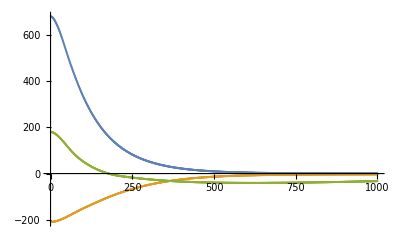

```mathematica
lim=1000;ListPlot[{ass["OCT"][[1;;lim]],ass["PINCH"][[1;;lim]],ass["BUCK"][[1;;lim]]},PlotRange->Full]
```